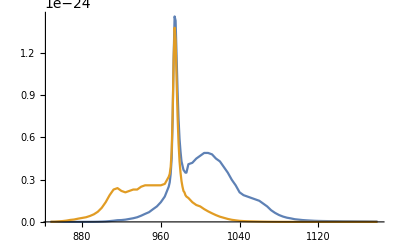

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]]];
σa=Interpolation[σ[[All,{1,3}]]];
```

```mathematica
(*Усилитель*)

τ2 = 1.05 10^-2;
τ3=10^-6;
τ5=1.4 10^-3;


NEr=300 6.62 10^22;
NYb=6000 6.62 10^22;

L=4;

c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 14^2 10^-12;(*Эффективная площадь моды*)

λs=1560;
λp=960;

σp45=2.6 10^-25;
σp54=1.4 10^-25;
σs12=1.052 10^-25;
σs21=1.683 10^-25;


Ps=Aeff h c/(λs 10^-9)
Pp=Aeff h c/(λp 10^-9)

Cac=0;
Ctr=10^7;
σESA=0;
Clear["Global`*"]

init=Solve[{ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ2+N3[z]/τ3(*-Cac N2[z]^2*)==0,
0==-N3[z]/τ3+Ctr N1[z]N5[z]-Ctr N3[z]N4[z],
0==-N5[z]/τ5-Ctr N1[z]N5[z]+Ctr N3[z]N4[z]+ρp[z](σp45 N4[z]-σp54 N5[z]),
ρs1[z]==ρs[z](σs21 N2[z]-σs12 N1[z](*-σESA N2[z]*)),
ρp1[z]==ρp[z](σp54 N5[z]-σp45 N4[z]),
N1[z]+N2[z]+N3[z]==NEr,
N4[z]+N5[z]==NYb,
ρp[z]==2/Pp,
ρs[z]==20 10^-3/Ps},
{ρp1[z],ρs1[z],N1[z],N2[z],N3[z],N4[z],N5[z],ρp[z],ρs[z]}]

τ2 = 1.05 10^-2;
τ3=10^-6;
τ5=1.4 10^-3;


NEr=300 6.62 10^22;
NYb=6000 6.62 10^22;

L=4;

c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 14^2 10^-12;(*Эффективная площадь моды*)

λs=1560;
λp=960;

σp45=2.6 10^-25;
σp54=1.4 10^-25;
σs12=1.052 10^-25;
σs21=1.683 10^-25;


Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

Cac=0;
Ctr=10^7;
σESA=0;



FindRoot[{ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ2+N3[z]/τ3(*-Cac N2[z]^2*)==0,
0==-N3[z]/τ3+Ctr N1[z]N5[z]-Ctr N3[z]N4[z],
0==-N5[z]/τ5-Ctr N1[z]N5[z]+Ctr N3[z]N4[z]+ρp[z](σp45 N4[z]-σp54 N5[z]),
ρs1[z]==ρs[z](σs21 N2[z]-σs12 N1[z](*-σESA N2[z]*)),
ρp1[z]==ρp[z](σp54 N5[z]-σp45 N4[z]),
N1[z]+N2[z]+N3[z]==NEr,
N4[z]+N5[z]==NYb,
ρp[z]==2/Pp,
ρs[z]==20 10^-3/Ps},{{ρs1[z],10^30},{ρp1[z],10^30},{ρp[z],2/Pp},{ρs[z],20 10^-3/Ps},{N1[z],10^30},{N2[z],10^30},{N3[z],10^30},{N4[z],10^30},{N5[z],10^30}},AccuracyGoal->-5
]

{N1[z],N2[z],N3[z],N4[z],N5[z],ρp[z],ρs[z]}/.init[[1]]
Thread[Equal[{N1[z],N2[z],N3[z],N4[z],N5[z],ρp[z],ρs[z]},%]]/.z->0
```

1.96271×10^-29

3.1894×10^-29

{{ρp1[z]→(-2 NYb σp45+42)/Pp,ρs1[z]→(-NEr Pp σs12 τ5+2 NYb σp45 σs12 τ2 τ5+20)/(50 Pp Ps τ5+Pp σs12 τ2 τ5+Pp σs21 τ2 τ5),N1[z]→(-50 NEr Pp Ps τ5+23)/(-50 Pp Ps τ5-Pp σs12 τ2 τ5-Pp σs21 τ2 τ5),N2[z]→1/(-50 Pp Ps τ5-Pp σs12 τ2 τ5-Pp σs21 τ2 τ5),N3[z]→-1/(Pp τ5),N4[z]→42+(√(1+1^2))/(2 (1)),N5[z]→(50 Pp Ps+23)/(2 (-50 Ctr Pp Ps τ2+Ctr Pp σs12 τ2 τ3-100 Ctr Ps σp45 τ2 τ5-100 4 τ5+2 Ctr σp45 σs12 τ2 τ3 τ5+2 Ctr σp54 σs12 τ2 τ3 τ5)),ρp[z]→2/Pp,ρs[z]→1/(50 Ps)},{1}}
 |  |  |  |

FindRoot::jsing: Encountered a singular Jacobian at the point {ρs1[z], ρp1[z], ρp[z], ρs[z], N1[z], N2[z], N3[z], N4[z], N5[z]} = {1.×10^30, 1.×10^30, 6.27076×10^28, 1.019×10^27, 1.×10^30, 1.×10^30, 1.×10^30, 1.×10^30, 1.×10^30}. Try perturbing the initial point(s).

{ρs1[z]→1.×10^30,ρp1[z]→1.×10^30,ρp[z]→6.27076×10^28,ρs[z]→1.019×10^27,N1[z]→1.×10^30,N2[z]→1.×10^30,N3[z]→1.×10^30,N4[z]→1.×10^30,N5[z]→1.×10^30}

{3.08987×10^21,1.98516×10^25,5.2948×10^21,1.46374×10^26,2.50826×10^26,6.27076×10^28,1.019×10^27}

{N1[0]==3.08987×10^21,N2[0]==1.98516×10^25,N3[0]==5.2948×10^21,N4[0]==1.46374×10^26,N5[0]==2.50826×10^26,ρp[0]==6.27076×10^28,ρs[0]==1.019×10^27}

```mathematica
{τ2,τ3,τ5,NEr,NYb,L,c,h,Aeff,λs,λp,σp45,σp54,σs12,σs21,Ps,Pp,Cac,Ctr,σESA}=Rationalize[{τ2,τ3,τ5,NEr,NYb,L,c,h,Aeff,λs,λp,σp45,σp54,σs12,σs21,Ps,Pp,Cac,Ctr,σESA},10^-40]

eq={ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ2+N3[z]/τ3(*-Cac N2[z]^2*)==0,
0==-N3[z]/τ3+Ctr N1[z]N5[z]-Ctr N3[z]N4[z],
0==-N5[z]/τ5-Ctr N1[z]N5[z]+Ctr N3[z]N4[z]+ρp[z](σp45 N4[z]-σp54 N5[z]),
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]-σESA N2[z]),
ρp'[z]==ρp[z](σp54 N5[z]-σp45 N4[z]),
N1[z]+N2[z]+N3[z]==NEr,
N4[z]+N5[z]==NYb,
ρp[0]==2/Pp,
ρs[0]==20 10^-3/Ps}

(*σp45=2.6 10^-25 NYb;
σp54=1.4 10^-25 NYb;
σs12=1.052 10^-25 NEr;
σs21=1.683 10^-25 NEr;
Ctr=10^7NYb NEr;
τ2 = 1.05 10^-2;
τ3=10^-6/NEr;
τ5=1.4 10^-3/NYb;

eq={ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ2+N3[z]/τ3(*-Cac N2[z]^2*)==0,
0==-N3[z]/τ3+Ctr N1[z]N5[z]-Ctr N3[z]N4[z],
0==-N5[z]/τ5-Ctr N1[z]N5[z]+Ctr N3[z]N4[z]+NYb ρp[z](σp45 N4[z]-σp54 N5[z]),
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z](*-σESA N2[z]*)),
ρp'[z]==ρp[z](σp54 N5[z]-σp45 N4[z]),
N1[z]+N2[z]+N3[z]==1,
N4[z]+N5[z]==1,
ρp[0]NYb==2/Pp,
ρs[0]NEr==20 10^-3/Ps};*)

sol=NDSolve[eq,
{ρp,ρs,N1,N2,N3,N4,N5},{z,0,L},AccuracyGoal->-27,PrecisionGoal->3,WorkingPrecision->2MachinePrecision,Method->{"TimeIntegration"->{"StateSpace", "BlockLowerTriangular"->"Ordering"}},MaxStepSize->0.1,StartingStepSize->0.01]

Through[{ρp,ρs,N1,N2,N3,N4,N5}[0]]/.z->0/.sol

(*sol=NDSolve[eq,
{ρp,ρs,N1,N2,N3,N4,N5},{z,0,L},AccuracyGoal->-25,Method -> {"IndexReduction"->Automatic,"DAEInitialization"-> {"QR"}}]

Through[{ρp,ρs,N1,N2,N3,N4,N5}[0]]/.z->0/.sol*)

Plot[Evaluate[{(*Pp ρp[z],Ps ρs[z],*)N4[z]/NYb,N5[z]/NYb,(N4[z]+N5[z])/NYb}/.sol],{z,0,0.5},PlotRange->All]
```

{21/2000,1/1000000,7/5000,19860000000000000729808896,397200000000000031776047104,4,300000000,1/1508295625942684586847070136774661,(49 π)/1000000000000,1560,960,1/3846153846153846175603119,1/7142857142857144339236188,1/9505703422053231884421743,1/5941770647653001206399927,1/50949961774116145267085885242,1/31353822630225327052178255394,0,10000000,0}

{-(2000 N2[z])/21+1000000 N3[z]+(N1[z]/9505703422053231884421743-N2[z]/5941770647653001206399927) ρs[z]==0,0==-1000000 N3[z]-10000000 N3[z] N4[z]+10000000 N1[z] N5[z],0==10000000 N3[z] N4[z]-(5000 N5[z])/7-10000000 N1[z] N5[z]+(N4[z]/3846153846153846175603119-N5[z]/7142857142857144339236188) ρp[z],ρs'[z]==(-N1[z]/9505703422053231884421743+N2[z]/5941770647653001206399927) ρs[z],ρp'[z]==(-N4[z]/3846153846153846175603119+N5[z]/7142857142857144339236188) ρp[z],N1[z]+N2[z]+N3[z]==19860000000000000729808896,N4[z]+N5[z]==397200000000000031776047104,ρp[0]==62707645260450654104356510788,ρs[0]==25474980887058072633542942621/25}

```mathematica
eqns={ρp[z](σp12 N1[z]-σp21 N2[z])+ρsr[z](σs12 N1[z]-σs21 N2[z])+ρsl[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ==0,
ρsr'[z]==ρsr[z](σs21 N2[z]-σs12 N1[z]),
ρsl'[z]==-ρsl[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN}
```

```mathematica
τ2 = 1.05 10^-2;
τ3=10^-6;
τ5=1.4 10^-3;


NEr=300 6.62 10^22;
NYb=600 6.62 10^22;

L=4;

c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 14^2 10^-12;(*Эффективная площадь моды*)

λs=1060;
λp=960;

σp45=2.6 10^-25;
σp54=1.4 10^-25;
σs12=1.052 10^-25;
σs21=1.683 10^-25;


Ps=Aeff h c/(λs 10^-9)
Pp=Aeff h c/(λp 10^-9)

Cac=0;
Ctr=10^7;
σESA=0;

σp12=σa[λp]
σp21=σe[λp];
σs12=σa[λs];
σs21=σe[λs];

eq={c/L D[N5[z,t],t]==-N5[z,t]/τ5+c ρp[z,t](σp12 N4[z,t]-σp21 N5[z,t]),
D[ρs[z,t],z]+1/L D[ρs[z,t],t]==ρs[z,t](σs21 N5[z,t]-σs12 N4[z,t]),
D[ρp[z,t],z]+1/L D[ρp[z,t],t]==ρp[z,t](σp21 N5[z,t]-σp12 N4[z,t]),
N4[z,t]+N5[z,t]==NYb,
ρs[z,0]==1/Ps Exp[-2 (z-L/8)^2/0.1^2] ,
ρp[z,0]==1/Pp Exp[-2 (z-L/2)^2/0.2^2],
N4[z,0]==NYb,N5[z,0]==0};

sol=NDSolve[{eq,ρs[L,t]==ρs[0,t],N4[L,t]==N4[0,t],N5[L,t]==N5[0,t]},{ρp,ρs,N4,N5},{z,0,L},{t,0,4},AccuracyGoal->-25]
```

2.88852×10^-29

3.1894×10^-29

2.6×10^-25

NDSolve::ndsz: At t == 0.501017, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 5.54816×10^10 at t = 0.501017 in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 351 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{ρp→InterpolatingFunction[{{…, 0., 4., …}, {0., 0.501017}}, <>],ρs→InterpolatingFunction[{{…, 0., 4., …}, {0., 0.501017}}, <>],N4→InterpolatingFunction[{{…, 0., 4., …}, {0., 0.501017}}, <>],N5→InterpolatingFunction[{{…, 0., 4., …}, {0., 0.501017}}, <>]}}

```mathematica
Plot3D[Evaluate[{Pp ρp[z,t]}/.sol],{t,0,4},{z,0,L},PlotRange->All,MaxRecursion->8]
Plot3D[Evaluate[{Ps ρs[z,t]}/.sol],{t,0,4},{z,0,L},PlotRange->All,MaxRecursion->8]
Plot3D[Evaluate[{N5[z,t]/NYb}/.sol],{t,0,4},{z,0,L},PlotRange->All,MaxRecursion->8]
```

2.88852×10^-29

3.1894×10^-29

NDSolve::eerr: Warning: scaled local spatial error estimate of 3422.92 at t = 4. in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 347 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{ρp→InterpolatingFunction[{{…, 0., 4., …}, {0., 4.}}, <>],ρs→InterpolatingFunction[{{…, 0., 4., …}, {0., 4.}}, <>],N4→InterpolatingFunction[{{…, 0., 4., …}, {0., 4.}}, <>],N5→InterpolatingFunction[{{…, 0., 4., …}, {0., 4.}}, <>]}}

-Graphics3D-

```mathematica
Manipulate[Plot[Evaluate[{ρp[z,t]Pp,ρs[z,t]Ps}/.sol],{z,0,L},PlotRange->{0,All}],{t,0,4}]
Manipulate[Plot[Evaluate[N5[z,t]/NYb/.sol],{z,0,L},PlotRange->{0,All}],{t,0,4}]
```